```mathematica
Get[ResourceFunction["NotebookRelativePath"][{"Packages", "Utils.wl"}]]
```

# Pulse Width Modulation (PWM)

## A prototype, self-teaching lesson with direct demonstrations

Egar Almeida

Flip Phillips & Daavid Väänänen

## Pre-requisites

Arduino

GPIO

digitalRead(), digitalWrite()

Electronics

Voltage, current, resistance

Ohm's law

Reading a waveform

Basic components

## Technical Explanation

## Frequency

We’ll begin the lesson by plotting a square wave

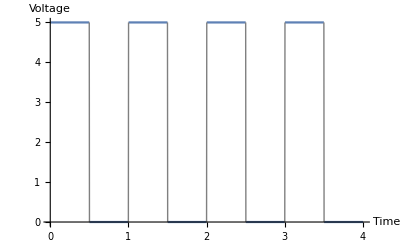

```mathematica
Plot[5 UnitStep[SquareWave[n]], {n,0,4},ExclusionsStyle-> Gray, AxesLabel->{"Time", "Voltage"}]
```

This square wave shows an alternation between 0 and 5 volts: We see 5 volts for a duration of half a second, then 0 volts for a duration of half a second.

This wave can be read as “a square wave of 1Hz with a 50% duty cycle”.

Hz (Hertz) is the frequency of the wave. 1Hz means 1 cycle per second.

Duty cycle is the portion of time during each cycle where the wave is at 5 volts, also known as “On” time (or HIGH in Arduino). 50% means that we have 5 volts for half the time and 0 volts for half the time.

If we were to connect an LED to a microcontroller pin outputting this wave, we’d get a blinking LED. In Arduino, we could do it with:

void loop() {
	digitalWrite(LED_PIN, HIGH);		// Turn LED on
	delay(500);					// Wait for 500 mS (half a second)
	digitalWrite(LED_PIN, LOW);		// Turn LED off
	delay(500);					// Wait for 500 mS again
}

This will produce the following result:

```mathematica
Animate[ledSymbolF[onOff], {onOff, 0, 1, 1}, DefaultDuration->1,]
```

What happens when we increase the frequency of this wave?
The LED would blink faster, but frequencies above 60hz would make it impossible for the human eye to distinguish the flickering due to flicker fusion and it’d seem like the LED is fully ON all the time.

Try varying the frequency of the square wave to see the waveform representation:

```mathematica
Manipulate[Column[{Style[IntegerPart[frequency] "Hz",20],Show[Plot[5 UnitStep[SquareWave[n*frequency]], {n,0,4},ExclusionsStyle->Gray, AxesLabel->{"Time", "Voltage"}], ImageSize->Medium]}], {frequency, 1, 10, 1},]
```

## Duty Cycle

Now that we’ve seen what altering the frequency does, let’s examine what happens when we alter the duty cycle between 10% and 100% at a constant frequency.

```mathematica
Manipulate[Column[{Style[IntegerPart[dutyCycle*100/1] "%", Large],Row[{Show[Plot[5squareWave[t,1,dutyCycle],{t,0,5}, ], ImageSize->Medium],Show[ledSymbolF[dutyCycle], ImageSize->Medium]}]}], {dutyCycle, .1, 1., .1}, SaveDefinitions->True]
```

By changing the duty cycle, you effectively change the time a device is in the ON state. The higher the duty cycle, the longer a device stays ON.

As you can observe in this simulation, the LED fades. This is one practical application of PWM.

PWM affects the average voltage and current according to the duty cycle of the wave. A 50% duty cycle will produce an output average voltage of 1/2 the input voltage.

The following example shows how to apply PWM to an LED using Arduino:

void loop() {
	analogWrite(LED_PIN, 128);		// Apply a 50% duty cycle wave to LED_PIN (analogWrite takes values from 0 to 255)
	delay(2000);					// Wait 2 seconds
	analogWrite(LED_PIN, 64);		// Apply a 25% duty cycle wave to LED_PIN
	delay(2000);					// Wait 2 seconds
}

## Applications

Switching power supplies

Rapid variations in pulse width, in combination with inductors and capacitors, are the basis for switching-based power supplies.

Motor speed control

By means of altering the average voltage and current, PWM can be an efficient method for motor speed controlling

Servo motor control

Variations in pulse width are what a hobby servo driver expects in order to determine the angle of its rotor and keep it at said angle. The driver expects a pulse every 20 mS, and the duration of said pulse (width) will determine the angle.

Audio

Variations in pulse width can generate digital audio effects.

Class D amplifiers operate in a similar fashion to a switching power supply in order to increase amplitude in sound waves.

## Demonstrations

## Setup

In order to demonstrate the concepts explained above, we are going to use Arduino. Connect an LED to pin 9 in series with a 220 Ohm resistor:

-Graphics-

Next, let’s do some setup. Enter the port where your Arduino is connected, here:

```mathematica
arduinoPort = "COM27";
```

Next, evaluate the following expression to connect to your Arduino:

```mathematica
arduino = DeviceOpen["Arduino", arduinoPort]
```

If everything worked correctly, your Arduino should be ready to receive commands.

## Frequency

Let’s start with the Frequency example. Input your desired frequency (in Hz) at the freq variable, then evaluate the expresion.

```mathematica
Module[
{freq=5},
Animate[
Column[
{ledSymbolF[onOff], DeviceWrite[arduino, 9-> onOff]}],{onOff, 0, 1, 1},
DefaultDuration->1/freq,
ContinuousAction->True,AppearanceElements->None
]
]
```

## Duty Cycle

Use the slider to change the duty cycle and watch the result on your LED.

```mathematica
Manipulate[Column[{DeviceWrite[arduino, 9-> dutyCycle],Style[IntegerPart[dutyCycle*100/1] "%", Large],Row[{Show[Plot[5squareWave[t,1,dutyCycle],{t,0,5}, ], ImageSize->Medium],Show[ledSymbolF[dutyCycle], ImageSize->Medium]}]}], {dutyCycle, .1, 1., .1}]
```

DeviceObject::ncdev: DeviceObject[{Arduino,1}] is not open.